```mathematica
basedir = "/Users/olav/Desktop/Doktorarbeit/Simulationen/Imaging/DemianTest/";
```

```mathematica
pos=<<(basedir<>"input/pos.mx");
connections=<<(basedir<>"input/cons.mx");
pars=<<(basedir<>"input/pars.mx")

(* calculate adjacency matrix *)
adjA=Table[0.0,{size/.pars},{size/.pars}];
For[ii=1,ii≤cons/.pars,ii++,
adjA⟦connections⟦ii,1⟧,connections⟦ii,2⟧⟧=1.0
];
adjA2=MatrixPower[adjA,2];

(* calculate degrees *)
degreein=Table[Total@adjA⟦All,ii⟧,{ii,size/.pars}];
degreeout=Table[Total@adjA⟦ii,All⟧,{ii,size/.pars}];
degreeboth=Diagonal@MatrixPower[adjA,2];
degreetotal=degreein+degreeout;
```

{size→100,cons→1200,mindist→0.01,cstrmin→0.1,cstrmax→0.1,thresh→1,topology→new,stepsize→0.5,leaktime→20,syndelay→0,transmittertime→100,transmitterred→0.3,allowbidircons→True,globalstimulation→False,globalconnectivity→False,nondirectionalcons→False,watchitmaxdur→110,analysislength→150,notes→watchit-Topologien fuer die NEST-Simulationen (Vergleich mit Demians TE-Auswertung),compiletime→15:03:36 on Aug 26 2009}

```mathematica
SetDirectory@basedir;
xfilename="te/transferentropy_os_15bins.mx";
adjAtransferentropy=<<(xfilename);
```

```mathematica
SetDirectory@basedir;
xfilename="granger/grangercausality_os_15bins.mx";
adjAtest=<<(xfilename);
```

```mathematica
adjAtest2=<<"granger/grangercausality_os_15bins_p1_global.mx";
```

```mathematica
SetDirectory@basedir;globaltransferentropy=<<"/Users/olav/Desktop/Doktorarbeit/Imaging/transferentropy/output/transferentropy_global.mx";
```

```mathematica
SetDirectory@basedir;maximatransferentropy=<<"/Users/olav/Desktop/Doktorarbeit/Imaging/transferentropy/output/transferentropy_maxima.mx";
```

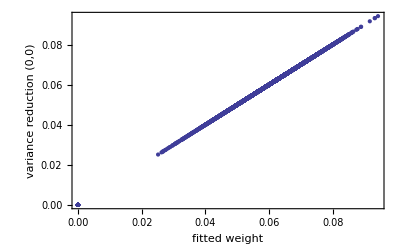

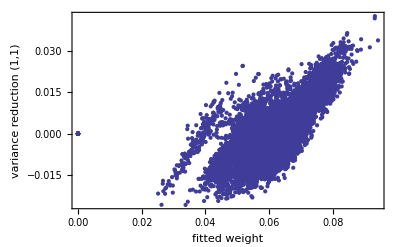

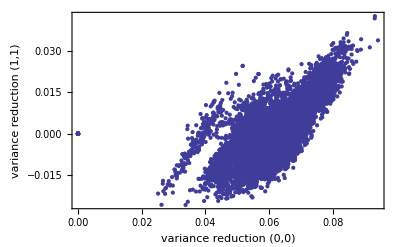

```mathematica
Clear[ii,jj];
ListPlot[Flatten[Table[{adjAtransferentropy⟦ii,jj⟧,adjAtest⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"fitted weight","variance reduction (0,0)"}]
ListPlot[Flatten[Table[{adjAtransferentropy⟦ii,jj⟧,adjAtest2⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"fitted weight","variance reduction (1,1)"}]
ListPlot[Flatten[Table[{adjAtest⟦ii,jj⟧,adjAtest2⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"variance reduction (0,0)","variance reduction (1,1)"}]
```

#### compare adjacency matrix directly

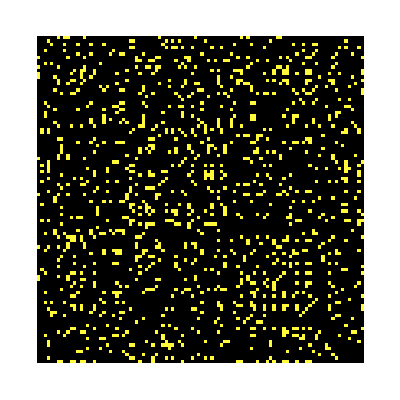

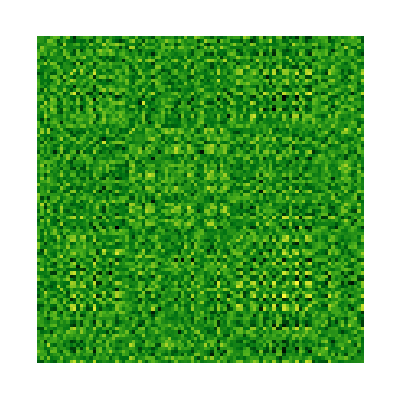

```mathematica
ArrayPlot[adjA,ColorFunction->"AvocadoColors"]
ArrayPlot[adjAtest2,ColorFunction->"AvocadoColors"]
(* ArrayPlot[maximatransferentropy,ColorFunction->"AvocadoColors"] *)
```

{m→0.011019,b→0.060452}

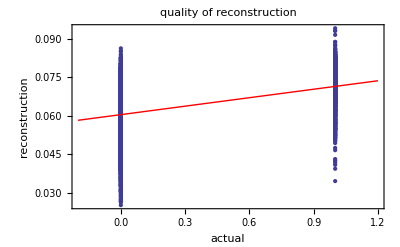

0.399863

```mathematica
(* compare single entries, 1st order *)
xdata=Drop[Sort@Flatten[Table[{adjA⟦ii,jj⟧,adjAtest⟦ii,jj⟧},{ii,Length@adjA},{jj,Length@adjA}],1],Length@adjA];
xfit=FindFit[xdata,m x+b,{m,b},x]
xplot={ListPlot[xdata,PlotRange->All],Plot[(m x+b)/.xfit,{x,-0.2,1.2},PlotStyle->Red]};
Show[xplot,FrameLabel->{"actual","reconstruction"},PlotLabel->"quality of reconstruction"]
Correlation[xdata⟦All,1⟧,xdata⟦All,2⟧]
```

```mathematica
Histogram3D[xdata(*,{Automatic,{0.002}}*),PlotRange->All,ImageSize->Large(*,PlotLabel->xfilename*)]
```

-Graphics3D-

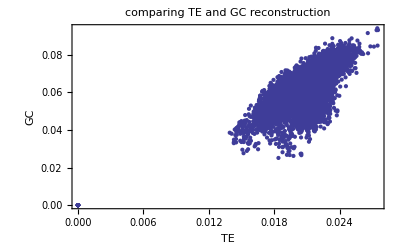

```mathematica
(* combine TE and GC results *)
ListPlot[Transpose@{Flatten@adjAtransferentropy,Flatten@xresult},PlotRange->Automatic,Frame->True,Axes->False,FrameLabel->{"TE","GC"},PlotLabel->"comparing TE and GC reconstruction"]

xdata=adjAtransferentropy/(Mean@adjAtransferentropy)+xresult/(Mean@xresult);
xdata=Drop[Sort@Flatten[Table[{adjA⟦ii,jj⟧,xdata⟦ii,jj⟧},{ii,Length@xdata},{jj,Length@xdata}],1],Length@xdata];
```

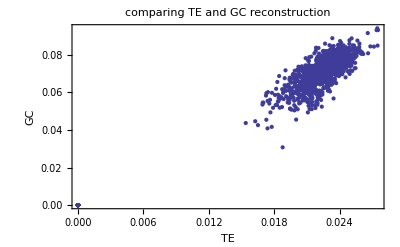

```mathematica
(* compare TE and GC results *)
ListPlot[Transpose@{Flatten@(adjAtransferentropy*adjA),Flatten@(xresult*adjA)},PlotRange->Automatic,Frame->True,Axes->False,FrameLabel->{"TE","GC"},PlotLabel->"comparing TE and GC reconstruction for present connections"]
```

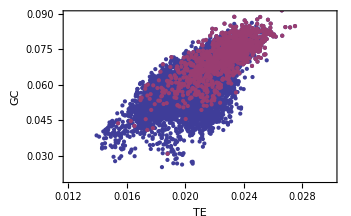

```mathematica
(* compare TE and GC results *)
ListPlot[{Transpose@{Flatten@adjAtransferentropy,Flatten@xresult},Transpose@{Flatten@(adjAtransferentropy*adjA),Flatten@(xresult*adjA)}},PlotRange->{{0.012,0.03},{0.02,0.09}},Frame->True,Axes->False,FrameLabel->{"TE","GC"}(*,PlotLabel->"comparing TE and GC reconstruction (present connections shown in red)",ImageSize->Large,PlotStyle->PointSize[Medium] *)]
```

#### plot ROC curves

```mathematica
xmin=Min@Last@Transpose@xdata;
xmax=Max@Last@Transpose@xdata;
xsteps=100;
xstepsize=(xmax-xmin)/xsteps;
(* go through all possible threshold values and compute the ROC data points *)
xROCpoints={};
For[xx=xmin,xx≤xmax,xx+=xstepsize,
xPresent=Length@Cases[xdata,{_?((Round@#==1)&),_}];
xPresentCorrect=Length@Cases[xdata,{_?((Round@#==1)&),_?((#>xx)&)}];
xAbsent=Length@Cases[xdata,{_?((Round@#==0)&),_}];
xAbsentIncorrect=Length@Cases[xdata,{_?((Round@#==0)&),_?((#>xx)&)}];
AppendTo[xROCpoints,{xAbsentIncorrect/xAbsent,xPresentCorrect/xPresent}];
];
Clear[xx,xmin,xmax,xsteps,xstepsize,xPresent,xPresentCorrect,xAbsent,xAbsentIncorrect];
```

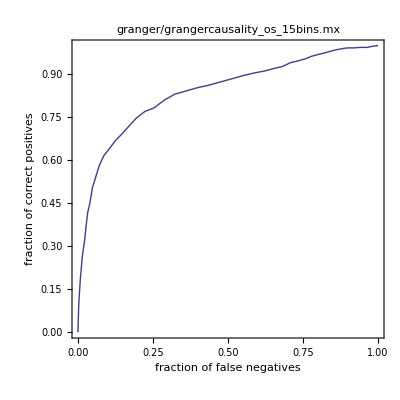

```mathematica
ListPlot[xROCpoints,Joined->True,Frame->True,Axes->False,AspectRatio->1,FrameLabel->{"fraction of false negatives","fraction of correct positives"},PlotLabel->xfilename]
```

```mathematica
xROCpointsGlobal=xROCpoints;
```

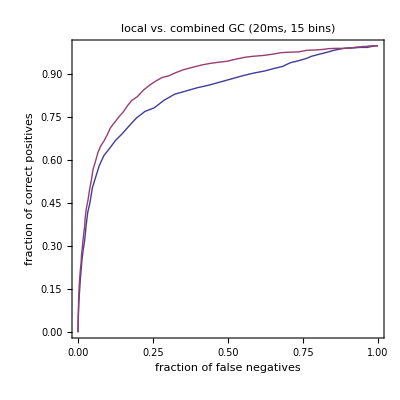

```mathematica
ListPlot[{xROCpoints,xROCpointsGlobal},Joined->True,Frame->True,Axes->False,AspectRatio->1,FrameLabel->{"fraction of false negatives","fraction of correct positives"},PlotLabel->"local vs. combined GC (20ms, 15 bins)"]
```

#### look for correlations (local)

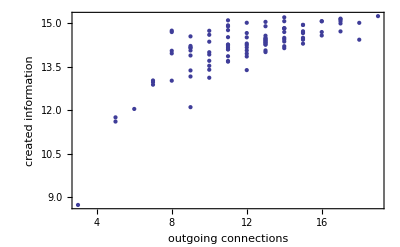

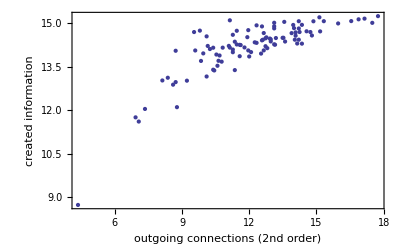

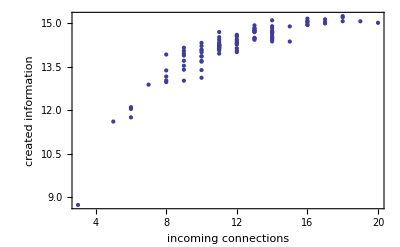

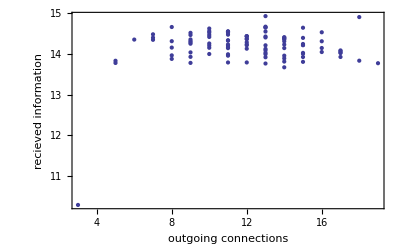

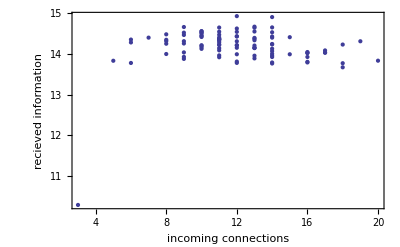

```mathematica
ListPlot[Table[{Total@adjA⟦ii⟧,Total@adjAtransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections","created information"}]
ListPlot[Table[{Sqrt@Total@adjA2⟦ii⟧,Total@adjAtransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections (2nd order)","created information"}]
ListPlot[Table[{Total@adjA⟦All,ii⟧,Total@adjAtransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections","created information"}]

ListPlot[Table[{Total@adjA⟦ii⟧,Total@adjAtransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections","recieved information"}]
ListPlot[Table[{Total@adjA⟦All,ii⟧,Total@adjAtransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections","recieved information"}]
```

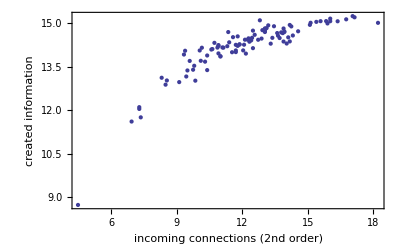

```mathematica
ListPlot[Table[{Sqrt@N@Total@adjA2⟦All,ii⟧,Total@adjAtransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections (2nd order)","created information"}]
```

#### extend to global TE

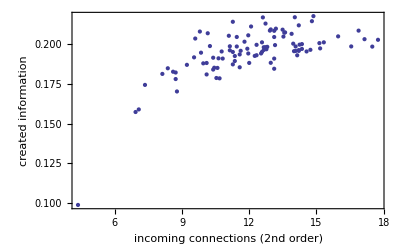

```mathematica
ListPlot[Table[{Sqrt@N@Total@adjA2⟦ii⟧,globaltransferentropy⟦ii,2⟧},{ii,Length@globaltransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections (2nd order)","recieved information from global"}]
```

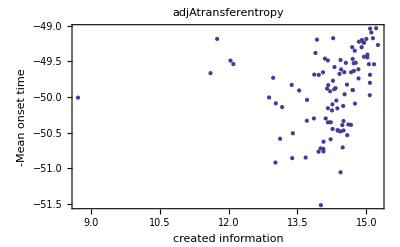

Correlation: 0.211251

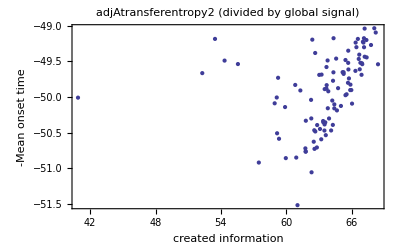

Correlation: 0.338019

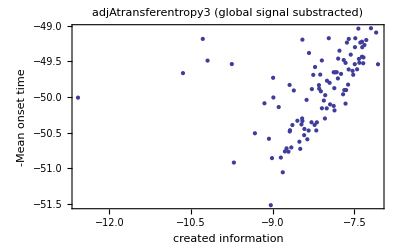

Correlation: 0.432565

```mathematica
adjAtransferentropy2=Table[adjAtransferentropy⟦ii,jj⟧/(globaltransferentropy⟦ii,1⟧+globaltransferentropy⟦jj,2⟧),{ii,100},{jj,100}];
adjAtransferentropy3=Table[adjAtransferentropy⟦ii,jj⟧-(globaltransferentropy⟦ii,1⟧+globaltransferentropy⟦jj,2⟧),{ii,100},{jj,100}];
ListPlot[{Table[{Total@adjAtransferentropy⟦ii⟧,-Mean@Drop[xtimes⟦ii,All,2⟧,1]},{ii,100}]},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"created information","-Mean onset time"},PlotLabel->"adjAtransferentropy"]
Print["Correlation: "<>ToString@Correlation[Table[Total@adjAtransferentropy⟦ii⟧,{ii,100}],Table[-Mean@Drop[xtimes⟦ii,All,2⟧,1],{ii,100}]]];

ListPlot[{Table[{Total@adjAtransferentropy2⟦ii⟧,-Mean@Drop[xtimes⟦ii,All,2⟧,1]},{ii,100}]},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"created information","-Mean onset time"},PlotLabel->"adjAtransferentropy2 (divided by global signal)"]
Print["Correlation: "<>ToString@Correlation[Table[Total@adjAtransferentropy2⟦ii⟧,{ii,100}],Table[-Mean@Drop[xtimes⟦ii,All,2⟧,1],{ii,100}]]];

ListPlot[{Table[{Total@adjAtransferentropy3⟦ii⟧,-Mean@Drop[xtimes⟦ii,All,2⟧,1]},{ii,100}]},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"created information","-Mean onset time"},PlotLabel->"adjAtransferentropy3 (global signal substracted)"]
Print["Correlation: "<>ToString@Correlation[Table[Total@adjAtransferentropy3⟦ii⟧,{ii,100}],Table[-Mean@Drop[xtimes⟦ii,All,2⟧,1],{ii,100}]]];
```

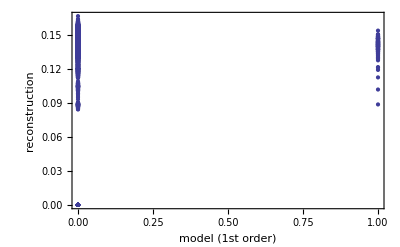

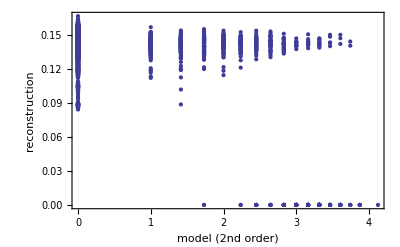

```mathematica
ListPlot[Flatten[Table[{adjA⟦ii,jj⟧,adjAtransferentropy⟦ii,jj⟧},{ii,Length@adjAtransferentropy},{jj,Length@adjAtransferentropy}],1],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"model (1st order)","reconstruction"}]
ListPlot[Flatten[Table[{Sqrt@adjA2⟦ii,jj⟧,adjAtransferentropy⟦ii,jj⟧},{ii,Length@adjAtransferentropy},{jj,Length@adjAtransferentropy}],1],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"model (2nd order)","reconstruction"}]
```

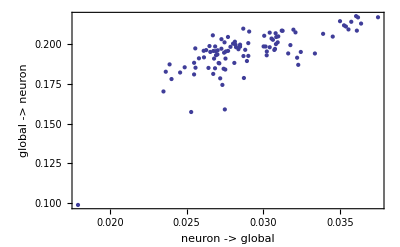

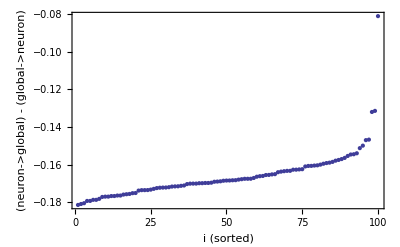

```mathematica
ListPlot[globaltransferentropy,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"neuron -> global","global -> neuron"}]
ListPlot[Sort[First@#-Second@#&/@globaltransferentropy],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"i (sorted)","(neuron->global) - (global->neuron)"}]
```

14.3058

14.4373

0.0302156

0.158886

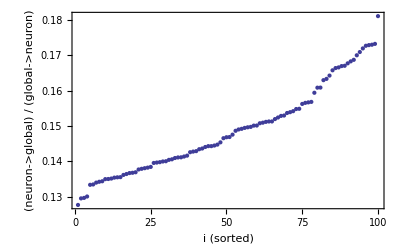

```mathematica
ii=2;
Total@adjAtransferentropy⟦ii,All⟧
Total@adjAtransferentropy⟦All,ii⟧
globaltransferentropy⟦ii,1⟧
globaltransferentropy⟦1,ii⟧

ListPlot[Sort[(First@#)/(Second@#)&/@globaltransferentropy],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"i (sorted)","(neuron->global) / (global->neuron)"}]
```

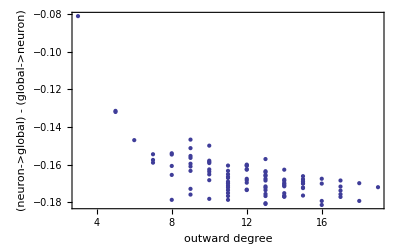

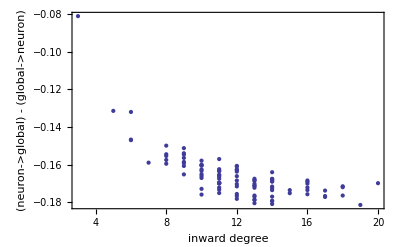

```mathematica
ListPlot[Table[{Total@adjA⟦ii⟧,globaltransferentropy⟦ii,1⟧-globaltransferentropy⟦ii,2⟧},{ii,Length@globaltransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outward degree","(neuron->global) - (global->neuron)"}]
ListPlot[Table[{Total@adjA⟦All,ii⟧,globaltransferentropy⟦ii,1⟧-globaltransferentropy⟦ii,2⟧},{ii,Length@globaltransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"inward degree","(neuron->global) - (global->neuron)"}]
```

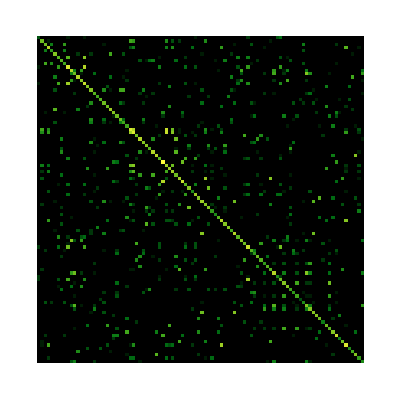

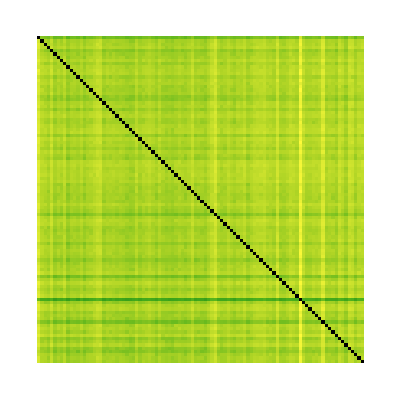

```mathematica
adjAtransferentropy2=Table[adjAtransferentropy⟦ii,jj⟧/(globaltransferentropy⟦ii,1⟧+globaltransferentropy⟦jj,2⟧),{ii,100},{jj,100}];
ArrayPlot[adjA2⟦1;;Length@adjAtransferentropy,1;;Length@adjAtransferentropy⟧,ColorFunction->"AvocadoColors"]
ArrayPlot[adjAtransferentropy2,ColorFunction->"AvocadoColors"]
```

#### examine maxima TE

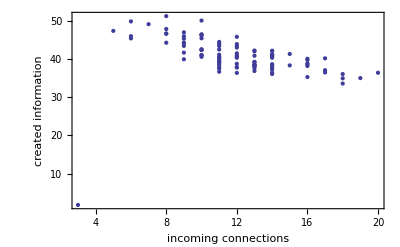

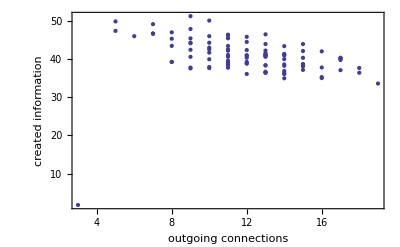

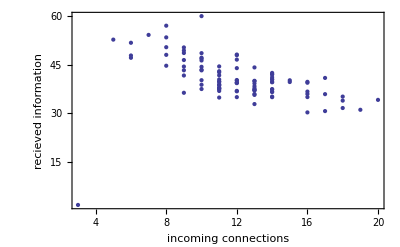

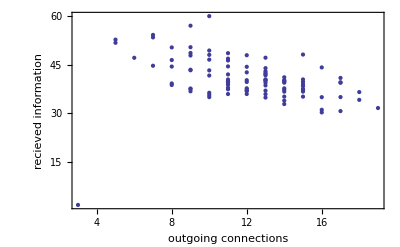

```mathematica
ListPlot[Table[{Total@adjA⟦All,ii⟧,Total@maximatransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections","created information"}]
ListPlot[Table[{Total@adjA⟦ii⟧,Total@maximatransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections","created information"}]

ListPlot[Table[{Total@adjA⟦All,ii⟧,Total@maximatransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections","recieved information"}]
ListPlot[Table[{Total@adjA⟦ii⟧,Total@maximatransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections","recieved information"}]
```

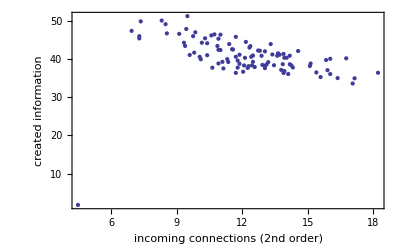

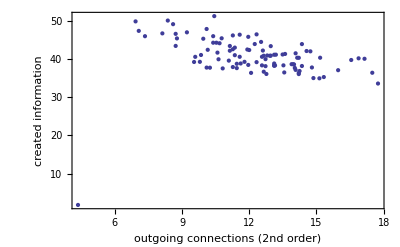

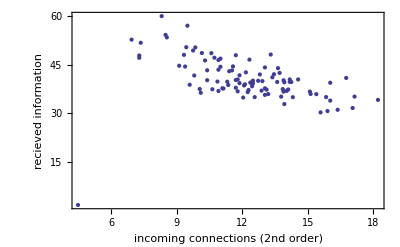

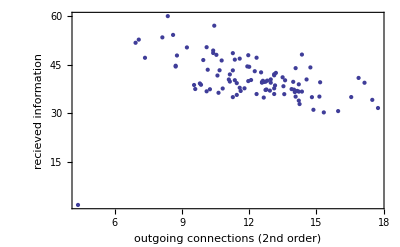

```mathematica
ListPlot[Table[{Sqrt@N@Total@adjA2⟦All,ii⟧,Total@maximatransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections (2nd order)","created information"}]
ListPlot[Table[{Sqrt@N@Total@adjA2⟦ii⟧,Total@maximatransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections (2nd order)","created information"}]

ListPlot[Table[{Sqrt@N@Total@adjA2⟦All,ii⟧,Total@maximatransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections (2nd order)","recieved information"}]
ListPlot[Table[{Sqrt@N@Total@adjA2⟦ii⟧,Total@maximatransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections (2nd order)","recieved information"}]
```

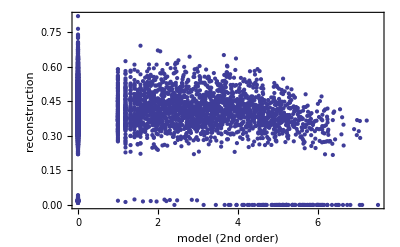

```mathematica
adjAx=N@(MatrixPower[adjA,4]^(1/4));
ListPlot[Flatten[Table[{adjAx⟦ii,jj⟧,maximatransferentropy⟦ii,jj⟧},{ii,Length@maximatransferentropy},{jj,Length@maximatransferentropy}],1],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"model (2nd order)","reconstruction"}]
```